## Project notes

### algorithmic ideas

greedy implementation

expanding radii and pushing (Lubachevsky–Stillinger algorithm)

jamming optimization

Molecular Dynamics packing implementation

### comparing algorithm convergence, time, packing fraction as function of step

### radial distribution of glassy system (level of periodicity)

### look at underlying crystal structure

## References

### Algorithmic

http://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.868.628&rep=rep1&type=pdf

https://en.wikipedia.org/wiki/Lubachevsky%E2%80%93Stillinger_algorithm

https://uwaterloo.ca/applied-mathematics/sites/ca.applied-mathematics/files/uploads/files/in-ting_ho.pdf

https://ac.els-cdn.com/S0925772117300172/1-s2.0-S0925772117300172-main.pdf?_tid=af9192c5-7b17-4015-a7bf-8691b2c620ff&acdnat=1530233551_fa2dba02fb911e6e281d0e28ea1629f0

https://ac.els-cdn.com/S0377221711003687/1-s2.0-S0377221711003687-main.pdf?_tid=ed44326a-996a-42bd-b8b5-76c083ff44f2&acdnat=1530234197_3052edb78817d71a6648e915b23efc20

https://ac.els-cdn.com/S0377221707004274/1-s2.0-S0377221707004274-main.pdf?_tid=877a6c4b-c11b-4eff-b124-27391056ce9d&acdnat=1530233557_a3f8c5e619ed8bb35db79d4b49a11eb6

https://link.springer.com/content/pdf/10.1057%2Fpalgrave.jors.2601836.pdf

https://arxiv.org/ftp/physics/papers/0405/0405089.pdf neighbor list collision-driven molecular dynamics simulation for nonspherical hard particles

### Mathematical

http://pi.math.cornell.edu/~connelly/ bobs page

https://link.springer.com/content/pdf/10.1007%2Fs00454-005-1172-4.pdf compact packings of the plane

https://www.cambridge.org/core/services/aop-cambridge-core/content/view/CAAA4EAA543E99B86183F27111A1EE72/S2050509414000243a.pdf/upper_bounds_for_packings_of_spheres_of_several_radii.pdf upper b for packing spheres of several radii

https://arxiv.org/pdf/1702.08442.pdf the isostatic conjecture, lattice and jammed packing theory

### Simulational

https://link.springer.com/content/pdf/10.1007%2Fs00454-003-0007-6.pdf some densest 2-size disc packings in the plane

https://arxiv.org/ftp/cond-mat/papers/0608/0608334.pdf Hypoconstrained jammed packings of Nonspherical Hard Particles: Ellipses and Ellipsoids

## Ideas and Scratch

take following functional form as force? consider potential barrier

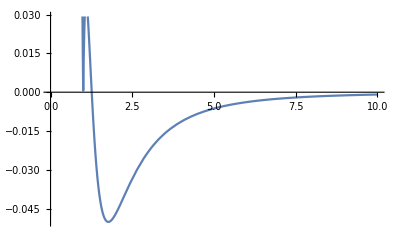

```mathematica
Plot[Abs[(x-1)](2-x^3)/x^7, {x, 0, 10}]
```

for contrast, lennard-jones force

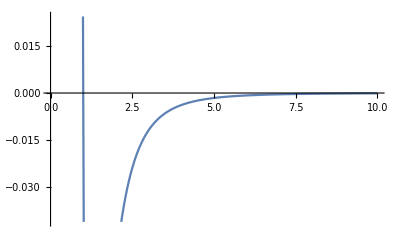

```mathematica
Plot[(1-x^3)/x^7, {x, 0, 10}, PlotRange->Automatic]
```

steepness problem? Maybe hard barrier when collision?

if dij=ri+rj set vi=vj=0